```mathematica
d={{1,1},{2,4},{5,1},{8,-4},{9,-3},{10,1},{11,1},{11.1,2},{11.4,4},{12,0}};
d=XY;{#[[2]],#[[1]]}&/@hedgeI;
n=Length[d]-1;(*Anzahl der Punkte - 1*)
p=10;(*Ordnung*)
m=n+1+p ;(*Anzahl der Knots - 1*)
(*Knot-Erzeugung*)
u=Join[Table[0,{i,p}],Table[i/(n+1-p),{i,0,n+1-p}],Table[1,{i,p}]];w=Table[1,{i,n+1}];
```

```mathematica
P[t0_]:=Module[{ab,a,k,j=m,i,t=t0,u=u,d=d*w,p=p,n=n,m=m,w=w},
(*j Bestimmtung*)
If[t==0,j=1,
While[t<=u[[j]],j--]];
If[j<=p,j=p+1];

ab=Table[{0,0},{i,n+1}];

(*Berechnung*)
For[k=1,k≤p,k++,
For[i=j-p+k,i≤j,i++,
a=(t-u[[i]])/(u[[i+p+1-k]]-u[[i]]);
ab[[i]]=(1-a)ab[[i-1]]+a ab[[i]]+(d[[i]]-d[[i-1]])/(u[[i+p+1-k]]-u[[i]]);
d[[i]]=(1-a)d[[i-1]]+a d[[i]];
w[[i]]=(1-a)w[[i-1]]+a w[[i]];
];
];
Append[d[[j]]/w[[j]],#[[2]]/#[[1]]&[ab[[j]]]]
]
```

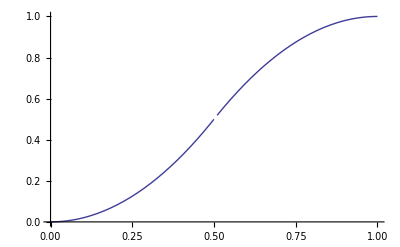

```mathematica
f[x_,n_]:=Piecewise[{{(2x)^n/2,x≤0.5}},-(2-2x)^n/2+1];Plot[f[x,2],{x,0,1}]
```

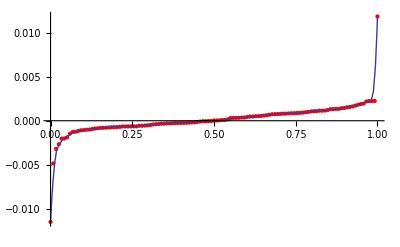

```mathematica
tt=Table[P[f[x,2]],{x,0,1,0.01}];ab=Transpose[tt][[3]];tt=Transpose[Transpose[tt][[1;;2]]];Show[ListPlot[d,PlotStyle->Red,PlotRange->All],ListPlot[tt,Joined->True,PlotRange->All]]
```

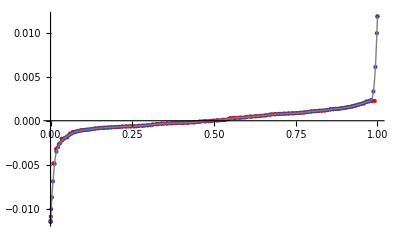

```mathematica
Show[ListPlot[d,Joined->False,PlotStyle->Red,PlotRange->All],ListPlot[tt,Joined->False,PlotRange->All],Plot[IP[x],{x,0,1},PlotStyle->Gray,PlotRange->All]]
```

```mathematica
IP[t0_]:=Module[{t=t0,tt=tt,j=Length[tt],m=ab,y},
(*j Bestimmtung*)
If[t==0,j=1,
While[t≤tt[[j,1]],j--]];
b=tt[[j+1,1]]-tt[[j,1]];y=t-tt[[j,1]];
{tt[[j,2]],tt[[j+1,2]],m[[j]],m[[j+1]]}.{1-(3 y^2)/b^2+(2 y^3)/b^3,(3 y^2)/b^2-(2 y^3)/b^3,y-(2 y^2)/b+y^3/b^2,-y^2/b+y^3/b^2}
]
```